```mathematica
??Degree
```

Degree gives the number of radians in one degree. It has a numerical value of π/180.

Attributes[°]={Constant,Protected,ReadProtected}

Z^n=r^n (Cos[n θ]+ⅈ Sin[n θ])

```mathematica
(1^83)Cos[83*(90 Degree)]+I*Sin[83*(90 Degree)]
```

-ⅈ

### Regiones el plano complejo y transformaciones

```mathematica
??RegionPlot
```

RowBox[{"RegionPlot", "[", RowBox[{StyleBox["pred", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] makes a plot showing the region in which StyleBox["pred", "TI"] is True.

Attributes[RegionPlot]={Protected,ReadProtected}

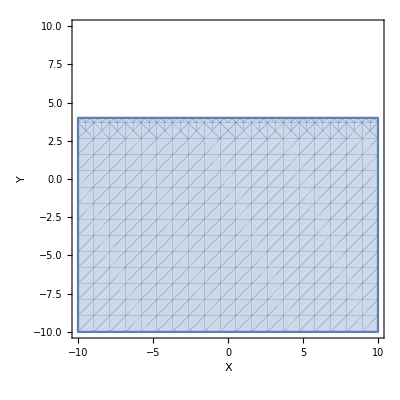

```mathematica
RegionPlot[y<4,{x,-10,10},{y,-10,10},Axes->True,AxesLabel->{X,Y}]
```

Bajo la transformacion Z=1/W

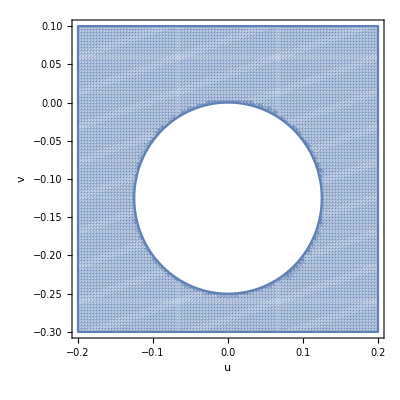

```mathematica
RegionPlot[(-v)/(u^2 +v^2)<4,{u,-.2,.2},{v,-.3,.1},PlotPoints->100, Axes->True,AxesLabel->{u,v},AspectRatio->Automatic]
```

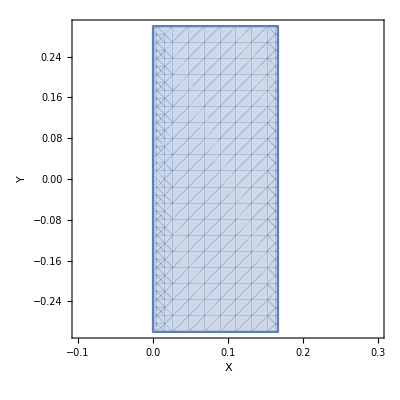

```mathematica
RegionPlot[0<x<(1/6),{x,-.1,.3},{y,-.3,.3},Axes->True,AxesLabel->{X,Y}]
```

Bajo la transformacion Z=1/W

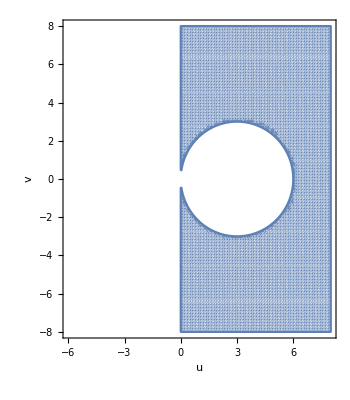

```mathematica
RegionPlot[0<(u/(u^2 +v^2))<(1/6),{u,-6,8},{v,-8,8},PlotPoints->100,AspectRatio->Automatic,Axes->True,AxesLabel->{u,v}]
```

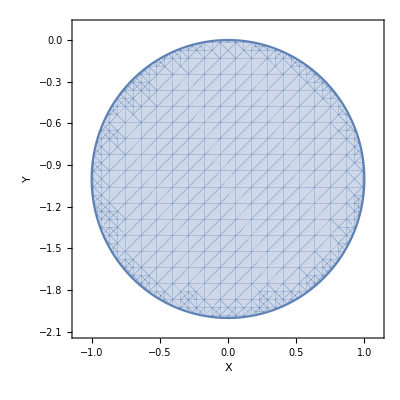

```mathematica
RegionPlot[x^2+(y+1)^2 <1,{x,-1.1,1.1},{y,-2.1,0.1},Axes->True,AxesLabel->{X,Y}]
```

Aplicamos una transformacion Z=1/W

```mathematica
(u/(u^2 +v^2))^2 + (-v/(u^2 +v^2)+1)^2//FullSimplify
```

1+(1-2 v)/(u^2+v^2)

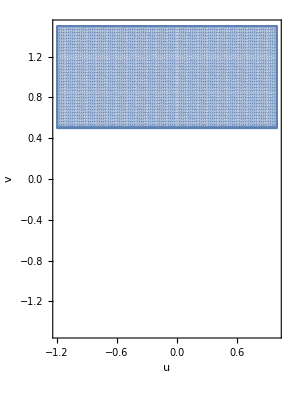

```mathematica
RegionPlot[1+(1-2 v)/(u^2+v^2)<1,{u,-1.2,1},{v,-1.5,1.5},PlotPoints->100, Axes->True,AxesLabel->{u,v},AspectRatio->Automatic]
```

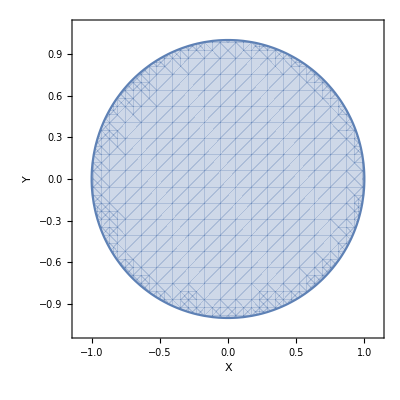

```mathematica
RegionPlot[Abs[x+I*y]<1,{x,-1.1,1.1},{y,-1.1,1.1},Axes->True,AspectRatio->Automatic,AxesLabel->{X,Y}]
```

Bajo la tgransformacion f(z)=2z-i

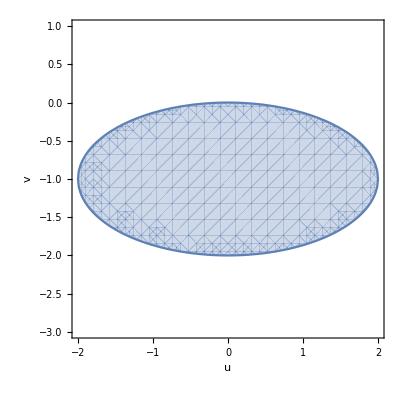

```mathematica
RegionPlot[((u^2)/4)+(v+1)^2 <1,{u,-2,2},{v,-3,1},Axes->True,AspectRatio->Automatic,AxesLabel->{u,v}]
```

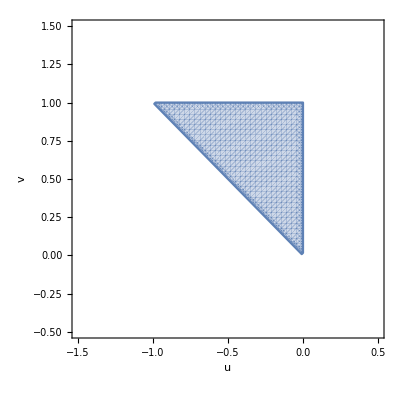

```mathematica
RegionPlot[v<1 && u<0 && v>-u,{u,-1.5,0.5},{v,-.5,1.5},PlotPoints->60,Axes->True,AspectRatio->Automatic,AxesLabel->{u,v}]
```